```mathematica
Needs["Wolfram`QuantumFramework`"];
Needs["Wolfram`QuantumFramework`SecondQuantization`"];  

Wolfram`QuantumFramework`SecondQuantization`SetFockSpaceSize[80];
```

```mathematica
ClearAll[ "Global`*"];
```

Basic definitions:

```mathematica
{X1,X2}=QuadratureOperators[];
X[θ_]:=X[θ]=QuantumOperator[Cos[θ] X1+Sin[θ] X2];

ψi[m_,r_,φ_,ϕ_]:=ψi[m,r,φ,ϕ]=Nest[SuperDagger[AnnihilationOperator[]]@#&,CatState[][<|α->N[r Exp[I φ]],ϕ->N[ϕ]|>],m]["Normalize"];

displaced[m_,r_,φ_,ϕ_,s_]:=displaced[m,r,φ,ϕ,s]=With[{ψ=ψi[m,r,φ,ϕ]},DisplacementOperator[#]@ψ&/@{N[s]/2,-N[s]/2}];

Φ[m_,r_,φ_,ϕ_,s_,δ1_,δ2_]:=With[{w=Exp[I N[δ1]] Tan[N[δ2]/2],ab=displaced[m,r,φ,ϕ,s]},((1+w) ab[[1]]+(1-w) ab[[2]])["Normalize"]];

dX2[m_,r_,φ_,ϕ_,s_,δ1_,δ2_,θ_]:=Re@OperatorVariance[Φ[m,r,φ,ϕ,s,δ1,δ2],X[θ]];

psucc[m_,r_,φ_,ϕ_,s_,δ1_,δ2_]:=With[{w=Exp[I N[δ1]] Tan[N[δ2]/2],ab=displaced[m,r,φ,ϕ,s]},Cos[N[δ2]/2]^2/4 (((1+w) ab[[1]]+(1-w) ab[[2]])["Norm"])^2];
```

Extra definitions:

```mathematica
Nm[m_,α_,ϕ_]:=2 m! (LaguerreL[m,-Abs[α]^2]+LaguerreL[m,Abs[α]^2] Exp[-2 Abs[α]^2] Cos[ϕ])
vonNeumann[m_,r_,φ_,ϕ_,s_,δ1_,δ2_]:=Module[{a=AnnihilationOperator[],f,u},f={Cos[N[δ2]/2],Exp[-ⅈ N[δ1]] Sin[N[δ2]/2]};u=MatrixExp[1/2 N[s] KroneckerProduct[PauliMatrix[1],Normal[(a["Dagger"]-a)["Matrix"]]]];Normalize[Conjugate[f].ArrayReshape[u.Flatten[KroneckerProduct[{1,0},Normal[ψi[m,r,φ,ϕ]["StateVector"]]]],{2,$FockSize}]]];
```

Parameters:

```mathematica
{r0,φ0,ϕ0,s0,δ10,δ20,m0,θ0}={2,Pi/2,Pi,0.5,Pi/2,8 Pi/9,2,0};
ms=Range[0,4];
ss={0,0.3,0.5,0.7,1.0};
θs={0,Pi/4,Pi/2,3 Pi/4,Pi};
d2s={1,3,5,7,8} Pi/9;
rs={0.5,1,2,3,4};
```

Helpers plotting:

```mathematica
lab[name_,vals_]:=Row[{name," = ",#}]&/@vals;
ylab=Row[{"(Δ",Subscript["X","θ"],").b2"}];
vac=GridLines->{Automatic,{{1/4,Directive[Dashed,Gray]}}};
```

# Three cat-state phases

Diagnostic: these three probabilities must be different

```mathematica
N[Table[{ph,psucc[1,1,π/2,ph,1,π/2,(8 π)/9]},{ph,{0,π/2,π}}]]
```

{{0.,0.837708},{1.5708,0.818424},{3.14159,0.79914}}

Only the relative cat-state phase ϕ is varied. The coherent-amplitude phase φ remains Pi/2. Fixed parameters: m = r = 1, delta1 = Pi/2; s = {0, 0.3, 0.5, 0.7, 1.0}. The original delta2 sampling is retained. All three plots use the same axes.

For these parameters, every curve passes through (delta2 = Pi/2, Ps = 1/2). At the sampled nonzero couplings, even > Yurke-Stoler > odd for delta2 > Pi/2; the order reverses for delta2 < Pi/2. The s = 0 curve is identical for all three states. Here m = r = 1 makes the Yurke-Stoler probability the arithmetic mean of the even and odd cases. 'Photon-added even/odd' names the parent cat: one photon addition reverses its photon-number parity.

## Photon-added even cat state: ϕ = 0

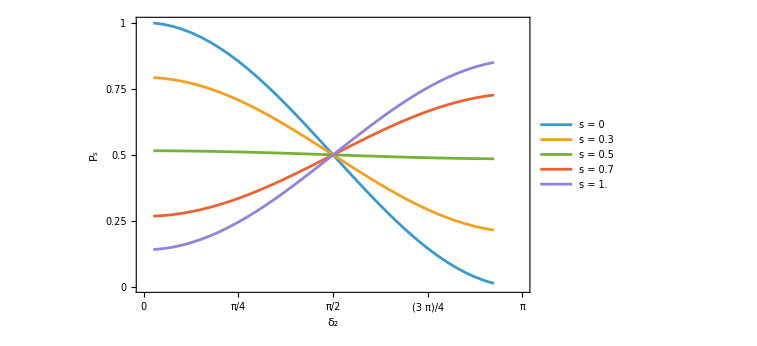

```mathematica
ListLinePlot[Table[Table[{δ2,psucc[1,1,φ0,0,s,δ10,δ2]},{δ2,π/40,(8.5 π)/9,π/40}],{s,ss}],PlotRange->{{0,π},{0,1}},PlotLegends->lab["s",ss],Frame->True,Axes->False,FrameLabel->{Subscript["δ", 2],Subscript["P", "s"]},FrameTicks->{{{0,0.25,0.5,0.75,1},None},{{0,π/4,π/2,(3 π)/4,π},None}},ImageSize->560,BaseStyle->{FontSize->13}]
```

## Photon-added Yurke–Stoler cat state: ϕ = π/2

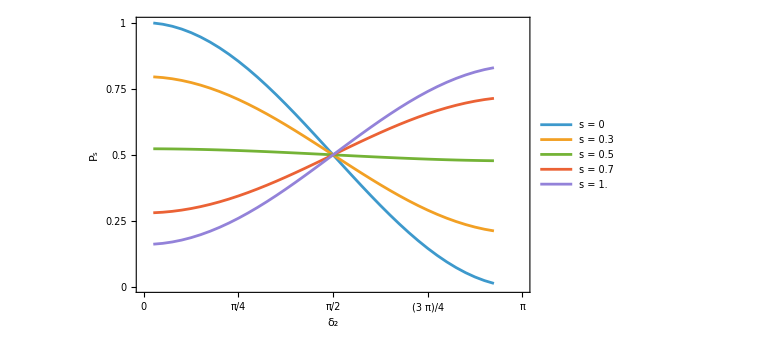

```mathematica
ListLinePlot[Table[Table[{δ2,psucc[1,1,φ0,π/2,s,δ10,δ2]},{δ2,π/40,(8.5 π)/9,π/40}],{s,ss}],PlotRange->{{0,π},{0,1}},PlotLegends->lab["s",ss],Frame->True,Axes->False,FrameLabel->{Subscript["δ", 2],Subscript["P", "s"]},FrameTicks->{{{0,0.25,0.5,0.75,1},None},{{0,π/4,π/2,(3 π)/4,π},None}},ImageSize->560,BaseStyle->{FontSize->13}]
```

## Photon-added odd cat state: ϕ = π

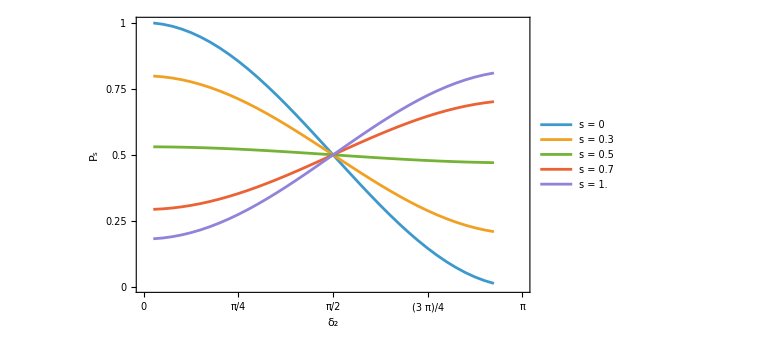

```mathematica
ListLinePlot[Table[Table[{δ2,psucc[1,1,φ0,π,s,δ10,δ2]},{δ2,π/40,(8.5 π)/9,π/40}],{s,ss}],PlotRange->{{0,π},{0,1}},PlotLegends->lab["s",ss],Frame->True,Axes->False,FrameLabel->{Subscript["δ", 2],Subscript["P", "s"]},FrameTicks->{{{0,0.25,0.5,0.75,1},None},{{0,π/4,π/2,(3 π)/4,π},None}},ImageSize->560,BaseStyle->{FontSize->13}]
```

## Fig.2-style three-phase composite and PNG export

Evaluate the original definitions above first, then evaluate the cells below. All original sampling points are retained. The PNG is saved beside this notebook.

```mathematica
data = ReleaseHold /@ {HoldComplete[Table[Table[{δ2, psucc[1, 1, φ0, 0, s, δ10, δ2]}, {δ2, Pi/40, (8.5*Pi)/9, Pi/40}], {s, ss}]], HoldComplete[Table[Table[{δ2, psucc[1, 1, φ0, Pi/2, s, δ10, δ2]}, {δ2, Pi/40, (8.5*Pi)/9, Pi/40}], {s, ss}]], HoldComplete[Table[Table[{δ2, psucc[1, 1, φ0, Pi, s, δ10, δ2]}, {δ2, Pi/40, (8.5*Pi)/9, Pi/40}], {s, ss}]]};
```

```mathematica
font = "Times New Roman"; pw = (86/25.4)*72 - 47; ph = 1.5*(0.64*pw + 45) - 45; colors = {RGBColor[1, 0.24, 0.24], RGBColor[0.16, 0.24, 1], RGBColor[0, 0.68, 0.18], RGBColor[1, 0.5, 0], RGBColor[0.7, 0, 0.74]};
```

```mathematica
styles = MapThread[Directive[#1, AbsoluteThickness[1.35], AbsoluteDashing[#2]] & , {colors, {{4, 2}, {1, 1.8}, {4, 2}, {4, 1.8, 1, 1.8}, {5, 2}}}];
```

```mathematica
mark[i_] := Graphics[{EdgeForm[Directive[colors[[i]], AbsoluteThickness[0.9]]], FaceForm[White], Switch[i, 1, Disk[], 2, Polygon[{{0, 1}, {-0.866, -0.5}, {0.866, -0.5}}], 3, Polygon[{{0, 1}, {1, 0}, {0, -1}, {-1, 0}}], 4, Rectangle[{-1, -1}, {1, 1}], 5, Polygon[{{0, -1}, {-0.866, 0.5}, {0.866, 0.5}}]]}, PlotRange -> {{-1.2, 1.2}, {-1.2, 1.2}}, ImagePadding -> 0, ImageSize -> 4, AspectRatio -> 1];
```

```mathematica
piLabel[n_, d_] := If[n == 0, "0", Row[{If[n == 1, "", n], "π/", d}]];
```

```mathematica
blank[t_] := ({#1[[1]], "", #1[[3]]} & ) /@ t; ticks[major_, minor_] := Join[({#1[[1]], #1[[2]], {0.017, 0}} & ) /@ major, ({#1, "", {0.009, 0}} & ) /@ Select[minor, Min[Abs[#1 - major[[All,1]]]] > 10^(-7) & ]];
```

```mathematica
xt = {ticks[Table[{n*(Pi/9), piLabel[n, 9]}, {n, 0, 8, 2}], Range[0, 17]*(Pi/18)], ticks[{{0, "0"}, {Pi/2, "π/2"}, {Pi, "π"}, {3*(Pi/2), "3π/2"}, {2*Pi, "2π"}}, Range[0, 40]*(Pi/20)], ticks[Table[{n, n}, {n, 0, 4}], Range[0, 20]/5]};
```

```mathematica
yt = Table[{n/20, If[Mod[n, 4] == 0 && n <= 20, NumberForm[N[n/20], {2, 1}, NumberPadding -> {"", "0"}], ""], {If[Mod[n, 4] == 0, 0.017, 0.009], 0}}, {n, 0, 23}];
```

```mathematica
labels = {(Row[{Style["s", Italic], " = ", #1}] & ) /@ {"0.0", "0.3", "0.5", "0.7", "1.0"}, (Row[{Style["r", Italic], " = ", #1}] & ) /@ {"0.5", "1", "2", "3", "4"}, (Row[{Subscript[Style["δ", Italic], 2], " = ", piLabel[#1, 9]}] & ) /@ {1, 3, 5, 7, 8}};
```

```mathematica
legend[i_] := Grid[Flatten /@ Partition[Table[{Graphics[{styles[[k]], Line[{{0, 0.5}, {1, 0.5}}], Inset[mark[k], {0.5, 0.5}, Center, Offset[{4, 4}]]}, PlotRange -> {{0, 1}, {0, 1}}, ImagePadding -> 0, ImageSize -> {If[i == 2, 12, 19], 7}], labels[[i,k]]}, {k, 5}], If[i == 2, 3, 2], If[i == 2, 3, 2], 1, {}], Alignment -> {Left, Center}, Spacings -> {0.4, 0.06}, BaseStyle -> {FontFamily -> font, FontSize -> 10.5, Black}];
```

```mathematica
pw = 1.5*pw + 12; ph = 1.5*ph;
```

```mathematica
styles = styles /. {AbsoluteThickness[1.35] -> AbsoluteThickness[2.7]};
```

```mathematica
marker[i_] := mark[i] /. AbsoluteThickness[0.9] -> AbsoluteThickness[1.2];
```

```mathematica
major = {{0, "0"}, {2Pi/9, "2π/9"},{4Pi/9, "4π/9"},{6Pi/9, "6π/9"},{8Pi/9, "8π/9"}};
```

```mathematica
xTicks = ticks[major, Range[0, 40]*(Pi/40)];
```

```mathematica
yTicks = Table[{n/20, If[Mod[n, 4] == 0 && n <= 20, StringJoin[ToString[Quotient[n, 20]], ".", ToString[Mod[n/2, 10]]], ""], {If[Mod[n, 4] == 0, 0.017, 0.009], 0}}, {n, 0, 23}];
```

```mathematica
legendNew = Module[{entries, rows}, entries = Table[{Graphics[{styles[[k]], Line[{{0, 0.5}, {1, 0.5}}], Inset[marker[k], {0.5, 0.5}, Center, Offset[{6, 6}]]}, PlotRange -> {{0, 1}, {0, 1}}, ImagePadding -> 0, ImageSize -> {18, 10.5}], labels[[1,k]]}, {k, 5}]; rows = Partition[entries, 2, 2, 1, {}]; rows = Flatten /@ rows; rows[[-1]] = {Item[Row[{entries[[5,1]], Spacer[8], entries[[5,2]]}], Alignment -> Center], SpanFromLeft, SpanFromLeft, SpanFromLeft}; Grid[rows, Alignment -> Left, Spacings -> {0.25, 0.06}, BaseStyle -> {FontFamily -> font, FontSize -> 32, Black}]];
```

```mathematica
phaseTitles = (Style[Row[{Style["ϕ", Italic], " = ", #1}], FontFamily -> font, FontSize -> 40, Black] & ) /@ {"0", "π/2", "π"};
```

```mathematica
plotNew[d_, i_] := ListLinePlot[d, PlotStyle -> styles, Axes -> False, Frame -> True, FrameLabel -> {Subscript["δ", 2], If[i == 1, Subscript[Style["P", Italic], "s"], None]}, FrameTicks -> {{If[i == 1, yTicks, blank[yTicks]], blank[yTicks]}, {xTicks, blank[xTicks]}}, FrameStyle -> Directive[Black, AbsoluteThickness[1.6]], FrameTicksStyle -> Directive[Black, AbsoluteThickness[1.2], FontSize -> 32, FontFamily -> font], LabelStyle -> {FontFamily -> font, FontSize -> 38, Black, ScriptSizeMultipliers -> 0.85}, BaseStyle -> {FontFamily -> font, FontSize -> 25}, PlotRange -> {{0, Pi}, {0, 1.2}}, Sequence[PlotRangePadding -> None, GridLines -> {None, {1}}, GridLinesStyle -> Directive[GrayLevel[0.8], AbsoluteThickness[1.1], AbsoluteDashing[{5, 4}]]], ImagePadding -> {{If[i == 1, 102, 9], If[i == 3, 15, 9]}, {102, 48}}, ImageSize -> {pw + If[i == 1, 86, 9] + If[i == 3, 15, 9], ph + 125}, AspectRatio -> ph/pw, Background -> White, PlotRangeClipping -> False, Epilog -> Join[Flatten[Table[(Inset[marker[k], #1, Center, Offset[{6, 6}]] & ) /@ d[[k,DeleteDuplicates[Append[Range[1, Length[d[[k]]], 3], Length[d[[k]]]]]]], {k, 5}], 1], {Inset[Style[StringJoin["(", FromCharacterCode[96 + i], ")"], FontFamily -> font, FontSize -> 44, FontWeight -> Bold, Black], Scaled[{0.5, 0.13}], {Center, Center}], If[i == 1, Inset[legendNew, Scaled[{0.98, 0.98}], {Right, Top}], {}], Inset[phaseTitles[[i]], Offset[{0, 10}, Scaled[{0.5, 1}]], {Center, Bottom}]}]];
```

```mathematica
panels = MapIndexed[plotNew[#1, First[#2]] & , data];
```

```mathematica
widths = pw + {95, 18, 24}; h = ph + 125;
```

```mathematica
fig = Graphics[Table[Inset[panels[[i]], {Total[Take[widths, i - 1]], h}, {Left, Top}, {widths[[i]], h}], {i, 3}], PlotRange -> {{0, Total[widths]}, {0, h}}, ImagePadding -> 0, PlotRangePadding -> None, ImageSize -> {Total[widths], h}, AspectRatio -> h/Total[widths], Background -> White];
```

```mathematica
img = Rasterize[fig, "Image", RasterSize -> {4145, Automatic}, Background -> White];
```

```mathematica
pngPath = FileNameJoin[{NotebookDirectory[], "Fig.6.png"}];
```

```mathematica
Export[pngPath, img, "PNG", ImageResolution -> 300];
```

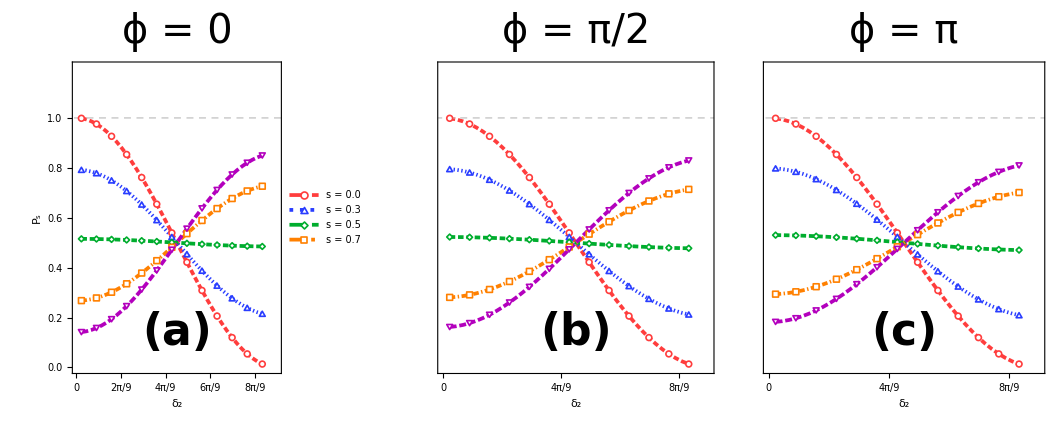

```mathematica
fig
```